```mathematica
Remove["Global`*"];
ClearAll["Global`*"];
Tstar[ii_,x_]:=Simplify[ChebyshevT[ii,2x-1]];
𝒳[frist_,end_,t_]:=Piecewise[{{1,frist≤t && t≤end}},0];
TT[mm_,x_]:=Piecewise[{{1/(√π),mm==0},{√(2/π)ChebyshevT[mm,x],mm>0}},0];
ψ[nn_,mm_,X_]:=Module[{x=X},
Return[Piecewise[{{2^((k+1)/2)TT[mm,2^(k+1)x-2(nn+1)],  nn/2^k≤ x && x≤ (nn+1)/2^k }},0]];
];
γ[mm_]:=Piecewise[{{2,mm== 0},{1,mm≥ 1}}];
Ψ[x_]:=Flatten[Table[ψ[i,j,x],{i,0,2^k-1},{j,0,M}]];
a[mm_,ii_]:=If[mm==0 && ii== 0,1,(-1)^ii 2^(2mm-2ii)(mm(2mm-ii-1)!)/(ii! (2mm-2ii)!)];
caputo[f_,{xx_,αα_},var_]:=Module[{nn=Ceiling[αα]},
If[!IntegerQ[αα],
Return[1/Gamma[nn-αα] Integrate[D[f/.xx->τ,{τ,nn}]/(var-τ)^(αα-nn+1),{τ,0,var},Assumptions->var>0]];
,
Return[D[f,{xx,nn}]/.Indeterminate->0];
];
];
w[mm_,nn_,qq_,αα_]:=Module[{},
Return[Piecewise[{{∑_(i=0)^mm 2^(k(mm-i))b[αα,mm,mm-i,qq]a[mm,i],nn== 0}},∑_(i=0)^mm ∑_(j=0)^(mm-i) b[αα,mm,j,qq]a[mm,i]Binomial[mm-i,j](-1)^(mm-i-j)2^(k j)nn^(mm-i-j)]];
];
Dstar[αα_,tt_]:=Module[{},
DαΨ=Flatten[Table[,{i,0,2^k-1},{j,0,M}]];
n=0;
For[m=0,m≤M,m++,
kk=n(M+1)+m+1;
DαΨ⟦kk⟧= 2^((k+1)/2)√(2/(π γ[m]))∑_(i=0)^m 2^(k(m-i))a[m,i]caputo[t^(m-i)Piecewise[{{1,0≤ t && t≤  1/2^k}},0],{t,αα},t];
];
For[n=1,n≤2^k-1,n++,
For[m=0,m≤M,m++,
kk=n(M+1)+m+1;
DαΨ⟦kk⟧= 2^((k+1)/2)√(2/(π γ[m]))∑_(i=0)^m ∑_(j=0)^(m-i) a[m,i]Binomial[m-i,j](-1)^(m-i-j)2^(k j)n^(m-i-j)caputo[t^j Piecewise[{{1,n/2^k≤ t && t≤  (n+1)/2^k}},0],{t,αα},t];
];
];
Return[Simplify[DαΨ]];
];
g[ii_,t_]:=Module[{},
α={gamma⟦ii⟧,gamma⟦ii⟧,gamma⟦ii⟧};
Return[Table[Simplify[caputo[yReal[t]⟦i⟧,{t,α⟦i⟧},t]-((f[t].(yReal[t]))⟦i⟧+Integrate[((t-s)^-β(K[t,s].(yReal[s])))⟦i⟧,{s,0,t},Assumptions->t>0])],{i,lenghtα}]];
];
MAIN[Λ_]:=Module[{},
α={gamma⟦Λ⟧,gamma⟦Λ⟧,gamma⟦Λ⟧};
lenghtα=Length[α];
c=Table[Subscript[CC, i ,j],{i,lenghtα},{j,2^k(M+1)}];
g[t_]=g[Λ,t];
Ans[t_]=Table[Simplify[-(c⟦i⟧.Dstar[α⟦i⟧,t])+g[t]⟦i⟧+(f[t].(c.Ψ[t]))⟦i⟧+Integrate[((t-s)^-β(K[t,s].(c.Ψ[s])))⟦i⟧,{s,0,t},Assumptions->t>0]],{i,lenghtα}];
chi=Solve[{ChebyshevT[2^k(M+1),2xx-1]==0,0≤ xx≤ 1},xx,Reals];
chi=N[xx/.chi];
For[i=1,i≤ 2^k(M+1),i++,Subscript[st, i]=chi⟦i⟧];
ans=Flatten[Simplify[Table[Ans[Subscript[st, i]],{i,2^k(M+1)}]]];
Cc=Flatten[Flatten[c]/.Solve[ans==0,Flatten[c]]];
yt[t_,gamma⟦Λ⟧]=Simplify[Partition[Cc,2^k(M+1)].Ψ[t]];
];
gamma={0.85,0.90,0.95,1};
(**************************************)
f[t_]={{0,0,1},{1,0,0},{0,0,1}};
β={1/2,1/3,1/4};
K[t_,s_]={{s t,1,0},{0,1,1},{1,s^2 t,0}};
y0={0,0,0};
yReal[t_]={t(t-1),t^2,t^3};
k=1;M=1;
(*********************************)
(*MAIN[1]
TimeObject[]
MAIN[2]
TimeObject[]
MAIN[3]
TimeObject[]*)
MAIN[3]
```

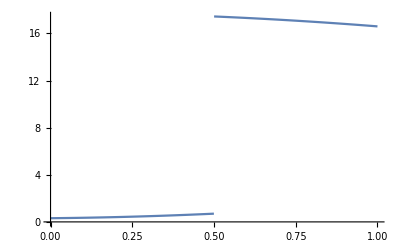

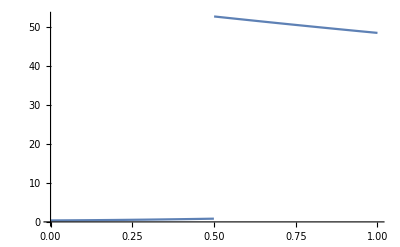

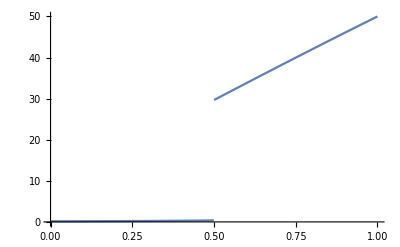

```mathematica
Plot[{Abs[yt[t,gamma⟦3⟧]⟦1⟧-yReal[t]⟦1⟧]},{t,0,1},PlotLegends->Automatic]
Plot[{Abs[yt[t,gamma⟦3⟧]⟦2⟧-yReal[t]⟦2⟧]},{t,0,1},PlotLegends->Automatic]
Plot[{Abs[yt[t,gamma⟦3⟧]⟦3⟧-yReal[t]⟦3⟧]},{t,0,1},PlotLegends->Automatic]
```

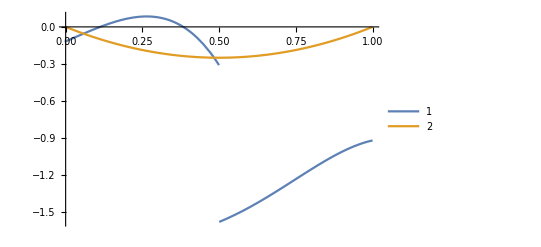

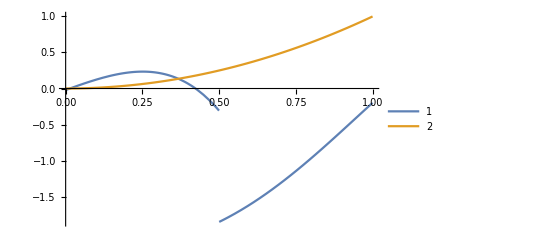

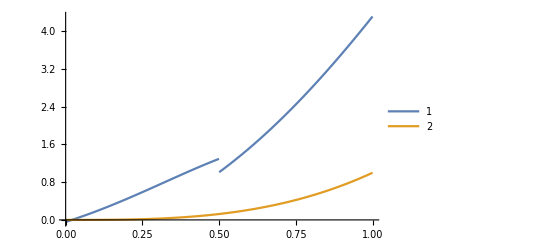

```mathematica
Plot[{yt[t,gamma⟦4⟧]⟦1⟧,yReal[t]⟦1⟧},{t,0,1},PlotLegends->Automatic]
Plot[{yt[t,gamma⟦4⟧]⟦2⟧,yReal[t]⟦2⟧},{t,0,1},PlotLegends->Automatic]
Plot[{yt[t,gamma⟦4⟧]⟦3⟧,yReal[t]⟦3⟧},{t,0,1},PlotLegends->Automatic]
```

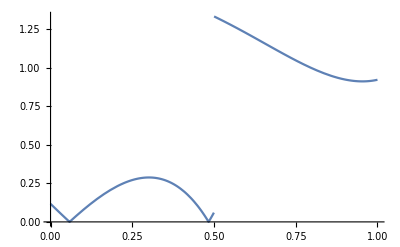

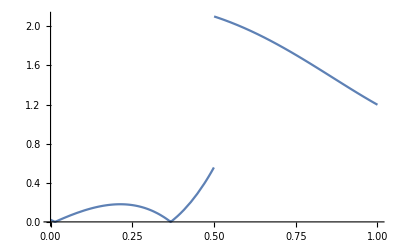

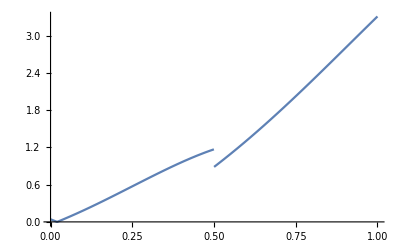

```mathematica
Plot[{Abs[yt[t,gamma⟦4⟧]⟦1⟧-yReal[t]⟦1⟧]},{t,0,1},PlotLegends->Automatic]
Plot[{Abs[yt[t,gamma⟦4⟧]⟦2⟧-yReal[t]⟦2⟧]},{t,0,1},PlotLegends->Automatic]
Plot[{Abs[yt[t,gamma⟦4⟧]⟦3⟧-yReal[t]⟦3⟧]},{t,0,1},PlotLegends->Automatic]
```

```mathematica
∫_0^1 Tstar[0,x] Tstar[0,x]/(√(1-(2x-1)^2))ⅆx
```

π/2